# Práctica 7

## Asignatura: Álgebra Fecha: 11/04/2023 Nombre: Ana León Pulido DNI: 21028026T

Ejercicio 1

```mathematica
NCOLORACIONES[matrizadyacencia_,lambda_]:=Module[{coloracionestemp,t,h,i,j,colorady,k},
coloraciones=Table[{k},{k,lambda}];
Do[
coloracionestemp={};
Do[
colorady={};
Do[
If[matrizadyacencia[[t,i]]==1 
,colorady=Union[colorady,{coloraciones[[h]][[t]]}]];
,{t,Length[coloraciones[[h]]]}];
Do[
If[Intersection[{j},colorady]=={},AppendTo[coloracionestemp,Append[coloraciones[[h]],j]]];
,{j,lambda}];
,{h,Length[coloraciones]}];
coloraciones=coloracionestemp;
,{i,2,Dimensions[matrizadyacencia][[1]]}];
coloraciones
];
```

```mathematica
NUMEROCROMATICO[matrizadyacencia_]:=Module[{},
t=1;
While[NCOLORACIONES[matrizadyacencia,t]=={},t++];
t]
```

```mathematica
PLANO[matrizadyacencia_]:=Module[{Nueva,k2,k3,subclados,lados},
Nueva=QUITARVERTICESGRADO210[matrizadyacencia];
tiempo=TimeUsed[];
plano=True;

vertices=Table[i,{i,Dimensions[Nueva][[1]]}];
lados={};

Do[
Do[
If[Nueva[[t1,t2]]==1,AppendTo[lados,t1->t2]];
,{t1,t2}];
,{t2,Dimensions[Nueva][[1]]}];

Do[
subclados=KSubsets[lados,k2];
Do[
If[HOMEOMORFOK5K33[MATRIZADYACENCIA[vertices,subclados[[k3]]]]==False,plano=False;subgrafo=subclados[[k3]];Break[]];
If[TimeUsed[]-tiempo>5,Print[k2-9," ",Length[subclados]-k3];tiempo=TimeUsed[];];
,{k3,Length[subclados]}];
If[!plano,Break[]];
,{k2,Length[lados],9,-1}];


plano
]
```

```mathematica
ARBOL[matrizadyacencia_]:=Module[{i,j,lados},
arbol=False;
If[CONEXO[matrizadyacencia],
arbol=(Dimensions[matrizadyacencia][[1]]==(Sum[matrizadyacencia[[i,j]],{i,Dimensions[matrizadyacencia][[1]]},{j,Dimensions[matrizadyacencia][[2]]}]/2)+1);
];
arbol
]
```

```mathematica
DIBUJAR[matrizadyacencia_]:=Module[{colores,colorear,COLORES,i},NUMEROCROMATICO[matrizadyacencia];colorear=coloraciones⟦1⟧;colores={"Negro","Rojo","Verde","Azul","Amarillo","Cyan","Marrón","Naranja","Púrpura","Rosa","Gris"};COLORES={Black,Red,Green,Blue,Yellow,Cyan,Brown,Orange,Purple,Pink,Gray};Print["Colores asignados: "];Do[Print["Vértice ",i,", color ",colores⟦colorear⟦i⟧⟧],{i,Length[colorear]}];GraphPlot[matrizadyacencia,VertexRenderingFunction->({COLORES⟦colorear⟦#2⟧⟧,Disk[#1,0.06],Black,Text[#2,{#1[[1]]+.1,#1[[2]]+.1}]}&)]
]
```

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

### a)

```mathematica
W1={1,2,3,4,5,6};
F1={1->2,2->3,3->6,6->5,5->4,4->1};
```

```mathematica
matrizadyacencia={{0,1,0,1,0,0},{1,0,1,0,0,0},{0,1,0,0,0,1},{1,0,0,0,1,0},{0,0,0,1,0,1},{0,0,1,0,1,0}};
```

```mathematica
NUMEROCROMATICO[matrizadyacencia]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

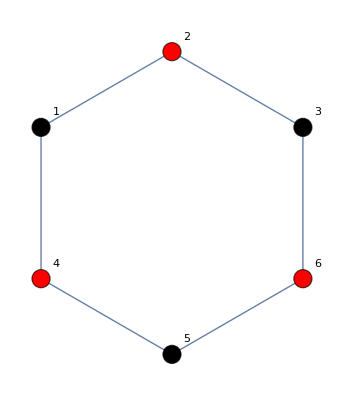

```mathematica
DIBUJAR[matrizadyacencia]
```

```mathematica
PLANO[matrizadyacencia]
```

True

```mathematica
ARBOL[matrizadyacencia]
```

False

```mathematica
W2={1,2,3,4,5,6};
F2={1->2,2->3,3->4,4->5,5->6,6->1};
```

```mathematica
A=MATRIZADYACENCIA[W2,F2];
```

```mathematica
NUMEROCROMATICO[A]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

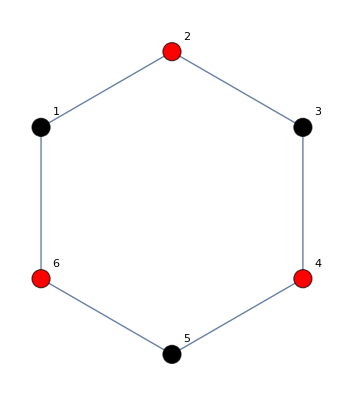

```mathematica
DIBUJAR[A]
```

```mathematica
PLANO[A]
```

True

```mathematica
ARBOL[A]
```

False

```mathematica
W3={1,2,3,4,5,6};
F3={1->6,2->4,3->5,4->3,5->1,6->2};
```

```mathematica
B=MATRIZADYACENCIA[W3,F3];
```

```mathematica
NUMEROCROMATICO[B]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

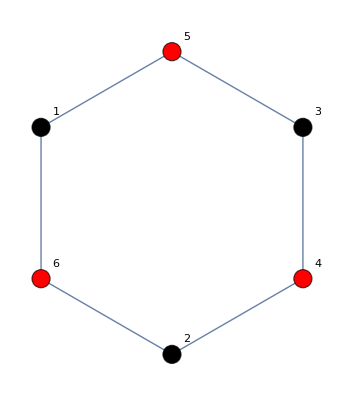

```mathematica
DIBUJAR[B]
```

```mathematica
PLANO[B]
```

True

```mathematica
ARBOL[B]
```

False

```mathematica
W4={1,2,3,4,5,6};
F4={1->6,2->1,3->4,4->5,5->6,6->2};
```

```mathematica
F=MATRIZADYACENCIA[W4,F4];
```

```mathematica
NUMEROCROMATICO[F]
```

3

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Verde

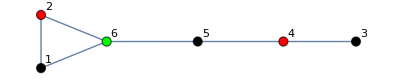

```mathematica
DIBUJAR[F]
```

```mathematica
PLANO[F]
```

True

```mathematica
ARBOL[F]
```

False

```mathematica
W5={1,2,3,4,5,6};
F5={1->6,2->5,3->4,1->2,3->5,4->6};
```

```mathematica
G=MATRIZADYACENCIA[W5,F5];
```

```mathematica
NUMEROCROMATICO[G]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Rojo

Vértice 4, color Negro

Vértice 5, color Negro

Vértice 6, color Rojo

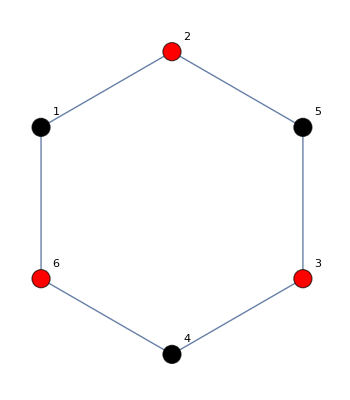

```mathematica
DIBUJAR[G]
```

```mathematica
PLANO[G]
```

True

```mathematica
ARBOL[G]
```

False

```mathematica
W6={1,2,3,4,5,6};
F6={1->2,1->3,2->3,3->5,4->5,4->6,5->6};
```

```mathematica
H=MATRIZADYACENCIA[W6,F6];
```

```mathematica
NUMEROCROMATICO[H]
```

3

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Negro

Vértice 5, color Rojo

Vértice 6, color Verde

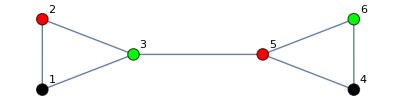

```mathematica
DIBUJAR[H]
```

```mathematica
PLANO[H]
```

True

```mathematica
ARBOL[H]
```

False

### b)Octógono

```mathematica
W8={1,2,3,4,5,6,7,8};
F8={1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1};
```

```mathematica
J=MATRIZADYACENCIA[W8,F8];
```

```mathematica
NUMEROCROMATICO[J]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Rojo

Vértice 7, color Negro

Vértice 8, color Rojo

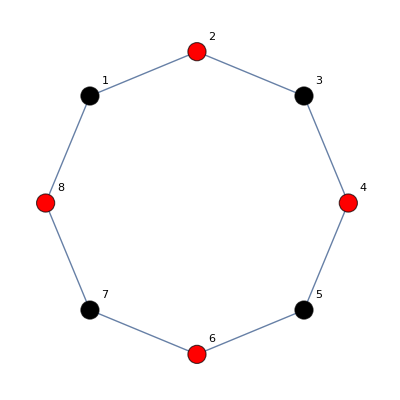

```mathematica
DIBUJAR[J]
```

```mathematica
PLANO[J]
```

True

```mathematica
ARBOL[J]
```

False

### c)K6

```mathematica
W7={1,2,3,4,5,6};
F7={2->1,3->1,4->1,5->1,6->1,1->2,3->2,4->2,5->2,6->2,1->3,2->3,4->3,5->3,6->3,1->4,2->4,3->4,5->4,6->4,
1->5,2->5,3->5,4->5,6->5,1->6,2->6,3->6,4->6,5->6};
```

```mathematica
L=MATRIZADYACENCIA[W7,F7];
```

```mathematica
NUMEROCROMATICO[L]
```

6

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Rojo

Vértice 3, color Verde

Vértice 4, color Azul

Vértice 5, color Amarillo

Vértice 6, color Cyan

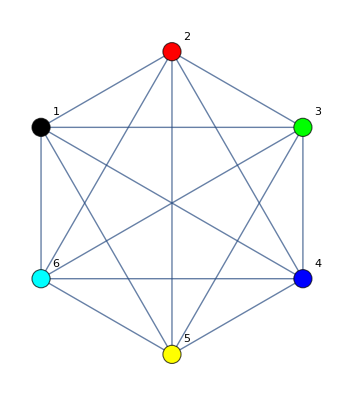

```mathematica
DIBUJAR[L]
```

```mathematica
PLANO[L]
```

True

```mathematica
ARBOL[L]
```

False

### d)K3,3

```mathematica
W9={1,2,3,4,5,6};
F9={1->4,1->5,1->6,2->4,2->5,2->6,3->4,3->5,3->6};
```

```mathematica
M=MATRIZADYACENCIA[W9,F9];
```

```mathematica
NUMEROCROMATICO[M]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Negro

Vértice 4, color Rojo

Vértice 5, color Rojo

Vértice 6, color Rojo

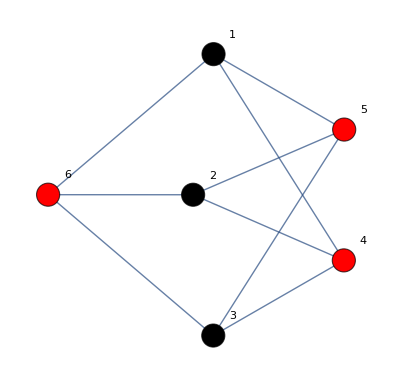

```mathematica
DIBUJAR[M]
```

```mathematica
PLANO[M]
```

True

```mathematica
ARBOL[M]
```

False

### e)

```mathematica
W10={1,2,3,4,5,6,7,8};
F10={1->3,1->7,2->4,2->8,3->5,4->6,5->7,6->8};
```

```mathematica
P=MATRIZADYACENCIA[W10,F10];
```

```mathematica
NUMEROCROMATICO[P]
```

2

Colores asignados:

Vértice 1, color Negro

Vértice 2, color Negro

Vértice 3, color Rojo

Vértice 4, color Rojo

Vértice 5, color Negro

Vértice 6, color Negro

Vértice 7, color Rojo

Vértice 8, color Rojo

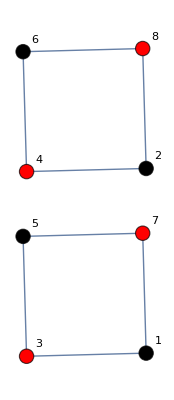

```mathematica
DIBUJAR[P]
```

```mathematica
PLANO[P]
```

True

```mathematica
ARBOL[P]
```

False